### Orbital Mechanics.Chapter2.Lagrangian Coefficients

#### Comparison between exact solution and approximate solution of planner orbit

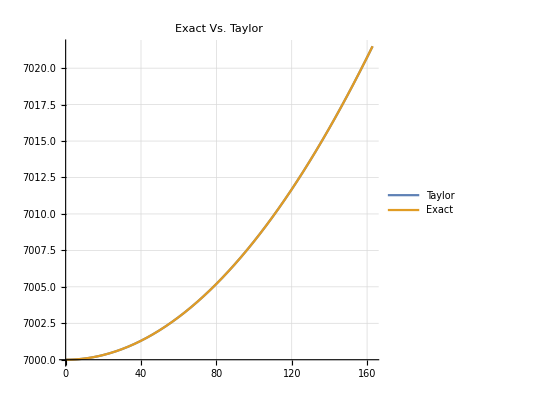

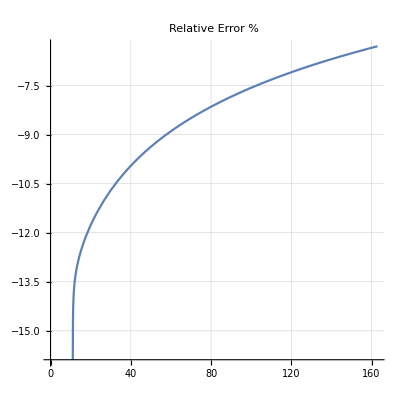

```mathematica
ClearAll[h]
μ=398600;
e=0.2;
Subscript[r, p]=7000;
(* Solve to get h of the orbit *)
h=(h/.NSolve[Subscript[r, p]==h^2/μ*1/(1+e Cos[0]),h])[[2]];
a=h^2/(μ(1-e^2));
(* Period of one cycle  *)
T=(2π)/(√μ)a^(3/2);
(* at perigee : there is no vlecity in redial component so :  *)
Subscript[v, p]=h/Subscript[r, p];
r0={Subscript[r, p],0,0};
v0={0,Subscript[v, p],0};
(* then calculate lagrange coefficients *)
f[t_]=1-μ/(2*Subscript[r, p]^3)*t^2+μ/2*(r0.v0)/Subscript[r, p]^5*t^3+μ/24((-2μ)/Subscript[r, p]^6+(3 Subscript[v, p]^2)/Subscript[r, p]^5-15*(r0.v0)^2/Subscript[r, p]^7)*t^4//N;
fdot[t_]=f'[t];
g[t_]=t-1/6*μ/Subscript[r, p]^3*t^3+μ/4*(r0.v0)/Subscript[r, p]^5*t^4//N;
r[t_]=Norm[f[t]*r0+g[t]*v0];
(*  Exact Solution using Ndsove*)
output=NDSolve[{R''[t]==(-μ R[t])/Norm[R[t]]^3,R'[0]==v0,R[0]==r0},R,{t,0,T},AccuracyGoal->10,PrecisionGoal->30];
Subscript[R, exact][t_]=Norm[Norm[R[t]/.output]];
tf=T/50;
(*Show[
     {ParametricPlot[{t,r[t]},{t,0,tf},PlotStyle->{Blue,Thick}],
      ParametricPlot[{t,Subscript[R, exact][t]},{t,0,tf},PlotStyle->{Red,Thick}]
     },
{GridLines->Automatic,ImageSize->Large,PlotLabel->"Exact Solution Vs Taylor",BaseStyle->{FontSize->12,Bold,Italic}}
    ]*)
ParametricPlot[{{t,r[t]},{t,Subscript[R, exact][t]}},{t,0,tf},PlotLegends->{"Taylor","Exact"},PlotLabel->"Exact Vs. Taylor",BaseStyle->{FontSize->12,Bold,Italic},GridLines->Automatic,AspectRatio->1]
ParametricPlot[{t,Log10[(Subscript[R, exact][t]-r[t])/Subscript[R, exact][t]]},{t,0,tf},PlotLabel->"Relative Error %",BaseStyle->{FontSize->12,Bold,Italic},GridLines->Automatic,AspectRatio->1]
```